```mathematica
f[n_] := 2^n
```

```mathematica
g[n_] := 2^n/(Sqrt[2*Pi*n])
```

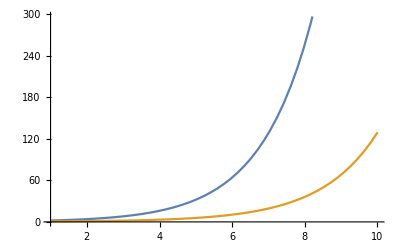

```mathematica
Plot[{f[n],g[n]},{n,1,10}]
```

```mathematica
Show[%15,ImageSize->Large]
```

Show::gtype: Symbol is not a type of graphics.

Show[Null,ImageSize→Large]

```mathematica
Show[%22,AxesLabel->{HoldForm[n],HoldForm[Executions]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Out is not a type of graphics.

Show[%22,AxesLabel→{n,Executions},PlotLabel→None,LabelStyle→{GrayLevel[0]}]

```mathematica
Export["/Users/jp/Documents/minhit-fig.pdf",%23,"PDF"]
```

/Users/jp/Documents/minhit-fig.pdf

```mathematica
Binomial[10,5]
```

252

```mathematica
Binomial[5,3]
```

10

```mathematica
Binomial[5,2]
```

10

```mathematica
Subsets[{1,2,3,4,5},{2}]
```

{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}

```mathematica
Subsets[{1,2,3,4,5},{3}]
```

{{1,2,3},{1,2,4},{1,2,5},{1,3,4},{1,3,5},{1,4,5},{2,3,4},{2,3,5},{2,4,5},{3,4,5}}

```mathematica
Subsets[{1,2,3,4,5,6,7,8,9,10},{5}]
```

{{1,2,3,4,5},{1,2,3,4,6},{1,2,3,4,7},{1,2,3,4,8},{1,2,3,4,9},{1,2,3,4,10},{1,2,3,5,6},{1,2,3,5,7},{1,2,3,5,8},{1,2,3,5,9},{1,2,3,5,10},{1,2,3,6,7},{1,2,3,6,8},{1,2,3,6,9},{1,2,3,6,10},{1,2,3,7,8},{1,2,3,7,9},{1,2,3,7,10},{1,2,3,8,9},{1,2,3,8,10},{1,2,3,9,10},{1,2,4,5,6},{1,2,4,5,7},{1,2,4,5,8},{1,2,4,5,9},{1,2,4,5,10},{1,2,4,6,7},{1,2,4,6,8},{1,2,4,6,9},{1,2,4,6,10},{1,2,4,7,8},{1,2,4,7,9},{1,2,4,7,10},{1,2,4,8,9},{1,2,4,8,10},{1,2,4,9,10},{1,2,5,6,7},{1,2,5,6,8},{1,2,5,6,9},{1,2,5,6,10},{1,2,5,7,8},{1,2,5,7,9},{1,2,5,7,10},{1,2,5,8,9},{1,2,5,8,10},{1,2,5,9,10},{1,2,6,7,8},{1,2,6,7,9},{1,2,6,7,10},{1,2,6,8,9},{1,2,6,8,10},{1,2,6,9,10},{1,2,7,8,9},{1,2,7,8,10},{1,2,7,9,10},{1,2,8,9,10},{1,3,4,5,6},{1,3,4,5,7},{1,3,4,5,8},{1,3,4,5,9},{1,3,4,5,10},{1,3,4,6,7},{1,3,4,6,8},{1,3,4,6,9},{1,3,4,6,10},{1,3,4,7,8},{1,3,4,7,9},{1,3,4,7,10},{1,3,4,8,9},{1,3,4,8,10},{1,3,4,9,10},{1,3,5,6,7},{1,3,5,6,8},{1,3,5,6,9},{1,3,5,6,10},{1,3,5,7,8},{1,3,5,7,9},{1,3,5,7,10},{1,3,5,8,9},{1,3,5,8,10},{1,3,5,9,10},{1,3,6,7,8},{1,3,6,7,9},{1,3,6,7,10},{1,3,6,8,9},{1,3,6,8,10},{1,3,6,9,10},{1,3,7,8,9},{1,3,7,8,10},{1,3,7,9,10},{1,3,8,9,10},{1,4,5,6,7},{1,4,5,6,8},{1,4,5,6,9},{1,4,5,6,10},{1,4,5,7,8},{1,4,5,7,9},{1,4,5,7,10},{1,4,5,8,9},{1,4,5,8,10},{1,4,5,9,10},{1,4,6,7,8},{1,4,6,7,9},{1,4,6,7,10},{1,4,6,8,9},{1,4,6,8,10},{1,4,6,9,10},{1,4,7,8,9},{1,4,7,8,10},{1,4,7,9,10},{1,4,8,9,10},{1,5,6,7,8},{1,5,6,7,9},{1,5,6,7,10},{1,5,6,8,9},{1,5,6,8,10},{1,5,6,9,10},{1,5,7,8,9},{1,5,7,8,10},{1,5,7,9,10},{1,5,8,9,10},{1,6,7,8,9},{1,6,7,8,10},{1,6,7,9,10},{1,6,8,9,10},{1,7,8,9,10},{2,3,4,5,6},{2,3,4,5,7},{2,3,4,5,8},{2,3,4,5,9},{2,3,4,5,10},{2,3,4,6,7},{2,3,4,6,8},{2,3,4,6,9},{2,3,4,6,10},{2,3,4,7,8},{2,3,4,7,9},{2,3,4,7,10},{2,3,4,8,9},{2,3,4,8,10},{2,3,4,9,10},{2,3,5,6,7},{2,3,5,6,8},{2,3,5,6,9},{2,3,5,6,10},{2,3,5,7,8},{2,3,5,7,9},{2,3,5,7,10},{2,3,5,8,9},{2,3,5,8,10},{2,3,5,9,10},{2,3,6,7,8},{2,3,6,7,9},{2,3,6,7,10},{2,3,6,8,9},{2,3,6,8,10},{2,3,6,9,10},{2,3,7,8,9},{2,3,7,8,10},{2,3,7,9,10},{2,3,8,9,10},{2,4,5,6,7},{2,4,5,6,8},{2,4,5,6,9},{2,4,5,6,10},{2,4,5,7,8},{2,4,5,7,9},{2,4,5,7,10},{2,4,5,8,9},{2,4,5,8,10},{2,4,5,9,10},{2,4,6,7,8},{2,4,6,7,9},{2,4,6,7,10},{2,4,6,8,9},{2,4,6,8,10},{2,4,6,9,10},{2,4,7,8,9},{2,4,7,8,10},{2,4,7,9,10},{2,4,8,9,10},{2,5,6,7,8},{2,5,6,7,9},{2,5,6,7,10},{2,5,6,8,9},{2,5,6,8,10},{2,5,6,9,10},{2,5,7,8,9},{2,5,7,8,10},{2,5,7,9,10},{2,5,8,9,10},{2,6,7,8,9},{2,6,7,8,10},{2,6,7,9,10},{2,6,8,9,10},{2,7,8,9,10},{3,4,5,6,7},{3,4,5,6,8},{3,4,5,6,9},{3,4,5,6,10},{3,4,5,7,8},{3,4,5,7,9},{3,4,5,7,10},{3,4,5,8,9},{3,4,5,8,10},{3,4,5,9,10},{3,4,6,7,8},{3,4,6,7,9},{3,4,6,7,10},{3,4,6,8,9},{3,4,6,8,10},{3,4,6,9,10},{3,4,7,8,9},{3,4,7,8,10},{3,4,7,9,10},{3,4,8,9,10},{3,5,6,7,8},{3,5,6,7,9},{3,5,6,7,10},{3,5,6,8,9},{3,5,6,8,10},{3,5,6,9,10},{3,5,7,8,9},{3,5,7,8,10},{3,5,7,9,10},{3,5,8,9,10},{3,6,7,8,9},{3,6,7,8,10},{3,6,7,9,10},{3,6,8,9,10},{3,7,8,9,10},{4,5,6,7,8},{4,5,6,7,9},{4,5,6,7,10},{4,5,6,8,9},{4,5,6,8,10},{4,5,6,9,10},{4,5,7,8,9},{4,5,7,8,10},{4,5,7,9,10},{4,5,8,9,10},{4,6,7,8,9},{4,6,7,8,10},{4,6,7,9,10},{4,6,8,9,10},{4,7,8,9,10},{5,6,7,8,9},{5,6,7,8,10},{5,6,7,9,10},{5,6,8,9,10},{5,7,8,9,10},{6,7,8,9,10}}

```mathematica
MyInter[m_]:= Print[Intersection[m,{1,3,4,5}]]
```

```mathematica
MyInter[{1,2,3,7}]
```

{1,3}

```mathematica
Scan[MyInter,Subsets[{1,2,3,4,5,6,7,8,9,10},{5}]]
```

{1,3,4,5}

{1,3,4}

{1,3,4}

{1,3,4}

«2 more identical outputs»

{1,3,5}

{1,3,5}

{1,3,5}

«2 more identical outputs»

{1,3}

{1,3}

{1,3}

«7 more identical outputs»

{1,4,5}

{1,4,5}

{1,4,5}

«2 more identical outputs»

{1,4}

{1,4}

{1,4}

«7 more identical outputs»

{1,5}

{1,5}

{1,5}

«7 more identical outputs»

{1}

{1}

{1}

«7 more identical outputs»

{1,3,4,5}

{1,3,4,5}

{1,3,4,5}

«2 more identical outputs»

{1,3,4}

{1,3,4}

{1,3,4}

«7 more identical outputs»

{1,3,5}

{1,3,5}

{1,3,5}

«7 more identical outputs»

{1,3}

{1,3}

{1,3}

«7 more identical outputs»

{1,4,5}

{1,4,5}

{1,4,5}

«7 more identical outputs»

{1,4}

{1,4}

{1,4}

«7 more identical outputs»

{1,5}

{1,5}

{1,5}

«7 more identical outputs»

{1}

{1}

{1}

«2 more identical outputs»

{3,4,5}

{3,4,5}

{3,4,5}

«2 more identical outputs»

{3,4}

{3,4}

{3,4}

«7 more identical outputs»

{3,5}

{3,5}

{3,5}

«7 more identical outputs»

{3}

{3}

{3}

«7 more identical outputs»

{4,5}

{4,5}

{4,5}

«7 more identical outputs»

{4}

{4}

{4}

«7 more identical outputs»

{5}

{5}

{5}

«7 more identical outputs»

{}

{}

{}

«2 more identical outputs»

{3,4,5}

{3,4,5}

{3,4,5}

«7 more identical outputs»

{3,4}

{3,4}

{3,4}

«7 more identical outputs»

{3,5}

{3,5}

{3,5}

«7 more identical outputs»

{3}

{3}

{3}

«2 more identical outputs»

{4,5}

{4,5}

{4,5}

«7 more identical outputs»

{4}

{4}

{4}

«2 more identical outputs»

{5}

{5}

{5}

«2 more identical outputs»

{}

```mathematica
h[n_]:= Binomial[n,Floor[n/2]]
```

```mathematica
h[10]
```

252

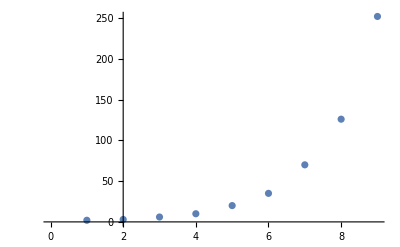

```mathematica
ListPlot[h[{2,3,4,5,6,7,8,9,10}],AxesOrigin->{2,0}]
```

```mathematica
h[{2,3,4,5,6,7,8,9,10}]
```

{2,3,6,10,20,35,70,126,252}

```mathematica
Print[h[Range[20]]]
```

{1,2,3,6,10,20,35,70,126,252,462,924,1716,3432,6435,12870,24310,48620,92378,184756}

```mathematica
h2[n_]:={n,h[n]}
```

```mathematica
n:=2
```

```mathematica
f1[j_]:=(1-n^(j+1))/(1-n)
```

```mathematica
f1[5]
```

63

```mathematica
g2[v_]:=Sum[f1[j],{j,v}]
```

```mathematica
g2[10]
```

4082

```mathematica
f1[9]
```

1023

```mathematica
g2[9]
```

2035

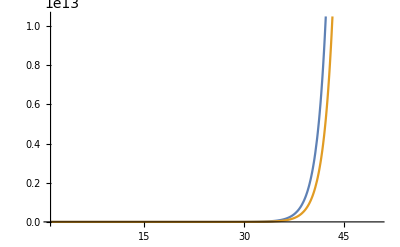

```mathematica
Plot[{f1[j],n^j},{j,1,50}]
```